```mathematica
Manipulate[ComplexListPlot[Map[I/(#+b I)&,Discard[Range[-10,10],#==0&]],PlotRange->{{-.25,.25},{-.5,.5}}],{b,-10,10,1}]
```

```mathematica
Manipulate[ComplexListPlot[Map[I/(a+# I)&,Discard[Range[-25,25],#==0&]],PlotRange->{{-.25,.25},{-.5,.5}}],{a,-25,25}]
```

```mathematica
Table[(a+b I),{a,-10,10,1},{b,-10,10,1}]
```

{{-10-10 ⅈ,-10-9 ⅈ,-10-8 ⅈ,-10-7 ⅈ,-10-6 ⅈ,-10-5 ⅈ,-10-4 ⅈ,-10-3 ⅈ,-10-2 ⅈ,-10-ⅈ,-10,-10+ⅈ,-10+2 ⅈ,-10+3 ⅈ,-10+4 ⅈ,-10+5 ⅈ,-10+6 ⅈ,-10+7 ⅈ,-10+8 ⅈ,-10+9 ⅈ,-10+10 ⅈ},{-9-10 ⅈ,-9-9 ⅈ,-9-8 ⅈ,-9-7 ⅈ,-9-6 ⅈ,-9-5 ⅈ,-9-4 ⅈ,-9-3 ⅈ,-9-2 ⅈ,-9-ⅈ,-9,-9+ⅈ,-9+2 ⅈ,-9+3 ⅈ,-9+4 ⅈ,-9+5 ⅈ,-9+6 ⅈ,-9+7 ⅈ,-9+8 ⅈ,-9+9 ⅈ,-9+10 ⅈ},{-8-10 ⅈ,-8-9 ⅈ,-8-8 ⅈ,-8-7 ⅈ,-8-6 ⅈ,-8-5 ⅈ,-8-4 ⅈ,-8-3 ⅈ,-8-2 ⅈ,-8-ⅈ,-8,-8+ⅈ,-8+2 ⅈ,-8+3 ⅈ,-8+4 ⅈ,-8+5 ⅈ,-8+6 ⅈ,-8+7 ⅈ,-8+8 ⅈ,-8+9 ⅈ,-8+10 ⅈ},{-7-10 ⅈ,-7-9 ⅈ,-7-8 ⅈ,-7-7 ⅈ,-7-6 ⅈ,-7-5 ⅈ,-7-4 ⅈ,-7-3 ⅈ,-7-2 ⅈ,-7-ⅈ,-7,-7+ⅈ,-7+2 ⅈ,-7+3 ⅈ,-7+4 ⅈ,-7+5 ⅈ,-7+6 ⅈ,-7+7 ⅈ,-7+8 ⅈ,-7+9 ⅈ,-7+10 ⅈ},{-6-10 ⅈ,-6-9 ⅈ,-6-8 ⅈ,-6-7 ⅈ,-6-6 ⅈ,-6-5 ⅈ,-6-4 ⅈ,-6-3 ⅈ,-6-2 ⅈ,-6-ⅈ,-6,-6+ⅈ,-6+2 ⅈ,-6+3 ⅈ,-6+4 ⅈ,-6+5 ⅈ,-6+6 ⅈ,-6+7 ⅈ,-6+8 ⅈ,-6+9 ⅈ,-6+10 ⅈ},{-5-10 ⅈ,-5-9 ⅈ,-5-8 ⅈ,-5-7 ⅈ,-5-6 ⅈ,-5-5 ⅈ,-5-4 ⅈ,-5-3 ⅈ,-5-2 ⅈ,-5-ⅈ,-5,-5+ⅈ,-5+2 ⅈ,-5+3 ⅈ,-5+4 ⅈ,-5+5 ⅈ,-5+6 ⅈ,-5+7 ⅈ,-5+8 ⅈ,-5+9 ⅈ,-5+10 ⅈ},{-4-10 ⅈ,-4-9 ⅈ,-4-8 ⅈ,-4-7 ⅈ,-4-6 ⅈ,-4-5 ⅈ,-4-4 ⅈ,-4-3 ⅈ,-4-2 ⅈ,-4-ⅈ,-4,-4+ⅈ,-4+2 ⅈ,-4+3 ⅈ,-4+4 ⅈ,-4+5 ⅈ,-4+6 ⅈ,-4+7 ⅈ,-4+8 ⅈ,-4+9 ⅈ,-4+10 ⅈ},{-3-10 ⅈ,-3-9 ⅈ,-3-8 ⅈ,-3-7 ⅈ,-3-6 ⅈ,-3-5 ⅈ,-3-4 ⅈ,-3-3 ⅈ,-3-2 ⅈ,-3-ⅈ,-3,-3+ⅈ,-3+2 ⅈ,-3+3 ⅈ,-3+4 ⅈ,-3+5 ⅈ,-3+6 ⅈ,-3+7 ⅈ,-3+8 ⅈ,-3+9 ⅈ,-3+10 ⅈ},{-2-10 ⅈ,-2-9 ⅈ,-2-8 ⅈ,-2-7 ⅈ,-2-6 ⅈ,-2-5 ⅈ,-2-4 ⅈ,-2-3 ⅈ,-2-2 ⅈ,-2-ⅈ,-2,-2+ⅈ,-2+2 ⅈ,-2+3 ⅈ,-2+4 ⅈ,-2+5 ⅈ,-2+6 ⅈ,-2+7 ⅈ,-2+8 ⅈ,-2+9 ⅈ,-2+10 ⅈ},{-1-10 ⅈ,-1-9 ⅈ,-1-8 ⅈ,-1-7 ⅈ,-1-6 ⅈ,-1-5 ⅈ,-1-4 ⅈ,-1-3 ⅈ,-1-2 ⅈ,-1-ⅈ,-1,-1+ⅈ,-1+2 ⅈ,-1+3 ⅈ,-1+4 ⅈ,-1+5 ⅈ,-1+6 ⅈ,-1+7 ⅈ,-1+8 ⅈ,-1+9 ⅈ,-1+10 ⅈ},{-10 ⅈ,-9 ⅈ,-8 ⅈ,-7 ⅈ,-6 ⅈ,-5 ⅈ,-4 ⅈ,-3 ⅈ,-2 ⅈ,-ⅈ,0,ⅈ,2 ⅈ,3 ⅈ,4 ⅈ,5 ⅈ,6 ⅈ,7 ⅈ,8 ⅈ,9 ⅈ,10 ⅈ},{1-10 ⅈ,1-9 ⅈ,1-8 ⅈ,1-7 ⅈ,1-6 ⅈ,1-5 ⅈ,1-4 ⅈ,1-3 ⅈ,1-2 ⅈ,1-ⅈ,1,1+ⅈ,1+2 ⅈ,1+3 ⅈ,1+4 ⅈ,1+5 ⅈ,1+6 ⅈ,1+7 ⅈ,1+8 ⅈ,1+9 ⅈ,1+10 ⅈ},{2-10 ⅈ,2-9 ⅈ,2-8 ⅈ,2-7 ⅈ,2-6 ⅈ,2-5 ⅈ,2-4 ⅈ,2-3 ⅈ,2-2 ⅈ,2-ⅈ,2,2+ⅈ,2+2 ⅈ,2+3 ⅈ,2+4 ⅈ,2+5 ⅈ,2+6 ⅈ,2+7 ⅈ,2+8 ⅈ,2+9 ⅈ,2+10 ⅈ},{3-10 ⅈ,3-9 ⅈ,3-8 ⅈ,3-7 ⅈ,3-6 ⅈ,3-5 ⅈ,3-4 ⅈ,3-3 ⅈ,3-2 ⅈ,3-ⅈ,3,3+ⅈ,3+2 ⅈ,3+3 ⅈ,3+4 ⅈ,3+5 ⅈ,3+6 ⅈ,3+7 ⅈ,3+8 ⅈ,3+9 ⅈ,3+10 ⅈ},{4-10 ⅈ,4-9 ⅈ,4-8 ⅈ,4-7 ⅈ,4-6 ⅈ,4-5 ⅈ,4-4 ⅈ,4-3 ⅈ,4-2 ⅈ,4-ⅈ,4,4+ⅈ,4+2 ⅈ,4+3 ⅈ,4+4 ⅈ,4+5 ⅈ,4+6 ⅈ,4+7 ⅈ,4+8 ⅈ,4+9 ⅈ,4+10 ⅈ},{5-10 ⅈ,5-9 ⅈ,5-8 ⅈ,5-7 ⅈ,5-6 ⅈ,5-5 ⅈ,5-4 ⅈ,5-3 ⅈ,5-2 ⅈ,5-ⅈ,5,5+ⅈ,5+2 ⅈ,5+3 ⅈ,5+4 ⅈ,5+5 ⅈ,5+6 ⅈ,5+7 ⅈ,5+8 ⅈ,5+9 ⅈ,5+10 ⅈ},{6-10 ⅈ,6-9 ⅈ,6-8 ⅈ,6-7 ⅈ,6-6 ⅈ,6-5 ⅈ,6-4 ⅈ,6-3 ⅈ,6-2 ⅈ,6-ⅈ,6,6+ⅈ,6+2 ⅈ,6+3 ⅈ,6+4 ⅈ,6+5 ⅈ,6+6 ⅈ,6+7 ⅈ,6+8 ⅈ,6+9 ⅈ,6+10 ⅈ},{7-10 ⅈ,7-9 ⅈ,7-8 ⅈ,7-7 ⅈ,7-6 ⅈ,7-5 ⅈ,7-4 ⅈ,7-3 ⅈ,7-2 ⅈ,7-ⅈ,7,7+ⅈ,7+2 ⅈ,7+3 ⅈ,7+4 ⅈ,7+5 ⅈ,7+6 ⅈ,7+7 ⅈ,7+8 ⅈ,7+9 ⅈ,7+10 ⅈ},{8-10 ⅈ,8-9 ⅈ,8-8 ⅈ,8-7 ⅈ,8-6 ⅈ,8-5 ⅈ,8-4 ⅈ,8-3 ⅈ,8-2 ⅈ,8-ⅈ,8,8+ⅈ,8+2 ⅈ,8+3 ⅈ,8+4 ⅈ,8+5 ⅈ,8+6 ⅈ,8+7 ⅈ,8+8 ⅈ,8+9 ⅈ,8+10 ⅈ},{9-10 ⅈ,9-9 ⅈ,9-8 ⅈ,9-7 ⅈ,9-6 ⅈ,9-5 ⅈ,9-4 ⅈ,9-3 ⅈ,9-2 ⅈ,9-ⅈ,9,9+ⅈ,9+2 ⅈ,9+3 ⅈ,9+4 ⅈ,9+5 ⅈ,9+6 ⅈ,9+7 ⅈ,9+8 ⅈ,9+9 ⅈ,9+10 ⅈ},{10-10 ⅈ,10-9 ⅈ,10-8 ⅈ,10-7 ⅈ,10-6 ⅈ,10-5 ⅈ,10-4 ⅈ,10-3 ⅈ,10-2 ⅈ,10-ⅈ,10,10+ⅈ,10+2 ⅈ,10+3 ⅈ,10+4 ⅈ,10+5 ⅈ,10+6 ⅈ,10+7 ⅈ,10+8 ⅈ,10+9 ⅈ,10+10 ⅈ}}

Power::infy: Infinite expression 1/0 encountered.

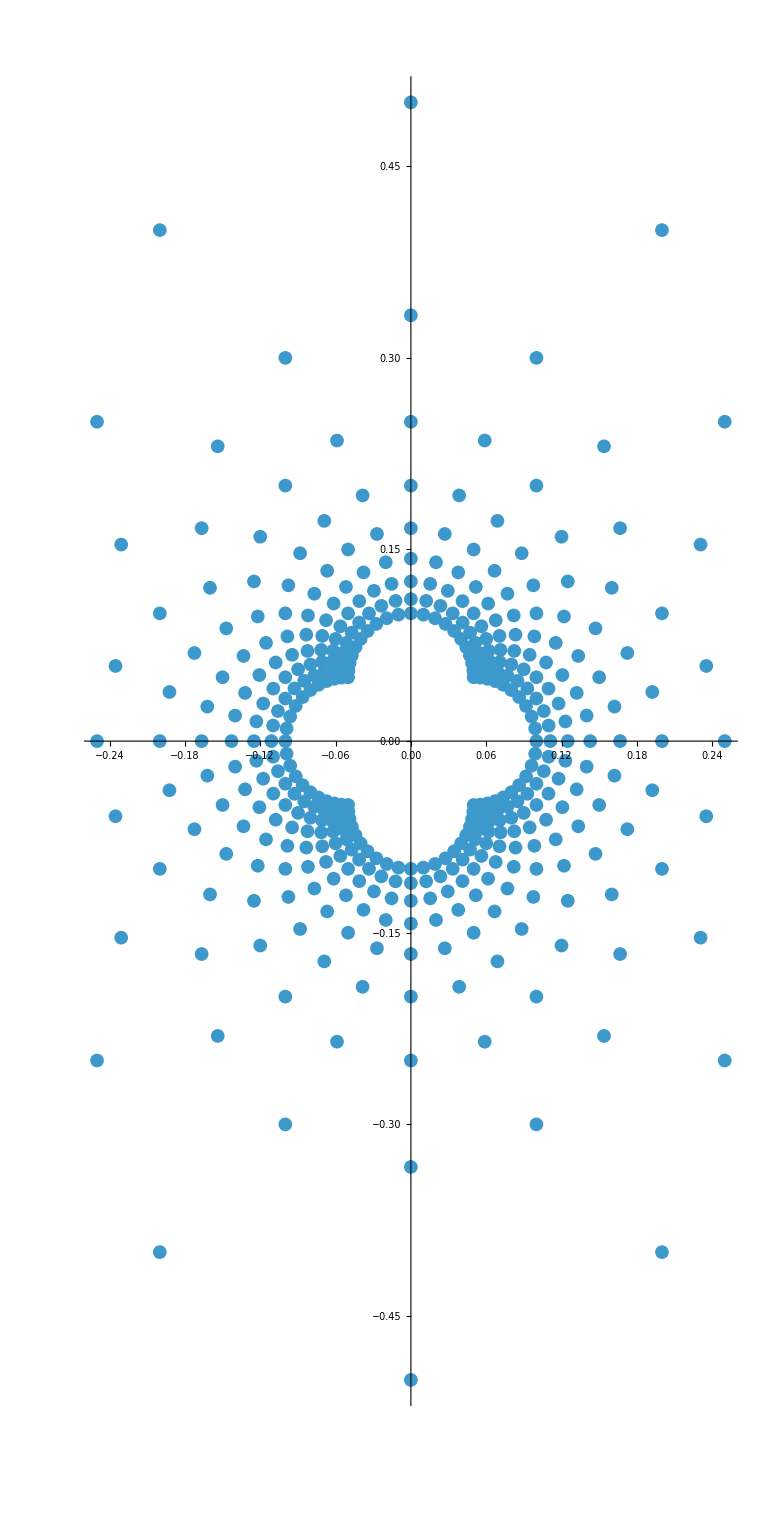

```mathematica
Show[Map[ComplexListPlot[#,ColorFunction->Function[{x, y, θ, r}, RandomColor[]]]&,Table[I/(a+b I),{a,-10,10,1},{b,-10,10,1}]],PlotRange->{{-.25,.25},{-.5,.5}}]
```